```mathematica
knownMass = 39.962590863; 
mUnknown = 36;
knownSecFreqs = 2*π*MHz*{.71, 1.3242, 1.6096}; (*Frequencies from Hao's Calibration on 06-04 - keep these and if need to change override later*)
massArr = {knownMass, mUnknown, knownMass};
EField ={0,0,0};
numIons = Length[massArr];
ionPositions = Table[{x[i], y[i], z[i]}, {i, numIons}];
ΩRF = 2*π*19.0696 * MHz;
```

```mathematica
qe = 1.60217663*10^-19;
e0 = 8.8541878188*10^-12;
kHz = 10^3;
MHz = 10^6;
nm = 10^-9;
μm = 10^-6;
mm = 10^-3;
amu = 1.66053904*10^-27;
r0 = 550 * μm;
κ = 0.077;
h = 6.62607015*10^-34;
ℏ = h/(2*π);
```

```mathematica
(*Calculate mass independent mathieu equations*)
getMathieuParams[knownSecFreqs_, knownMass_, ΩRF_]:= Module[{knownSecFreqsSorted, ar, az, qx},
knownSecFreqsSorted = knownSecFreqs[[Ordering[knownSecFreqs]]];
ar = 2/ΩRF^2*(knownSecFreqsSorted[[3]]^2-knownSecFreqsSorted[[2]]^2);
az = 4/ΩRF^2*knownSecFreqsSorted[[1]]^2;
qx = Sqrt[8*knownSecFreqsSorted[[3]]^2/ΩRF^2-(ar-2*az)];
{ar, az, qx}*knownMass
]
```

```mathematica
getMassIndepSecFreqs[massIndepMathieuParams_, massArr_, ΩRF_]:= Module[{arMassIndep, azMassIndep, qxMassIndep,
independentAxialFreqs, independentEGGsFreqs, independentRFFreqs},
arMassIndep = massIndepMathieuParams[[1]];
azMassIndep = massIndepMathieuParams[[2]];
qxMassIndep = massIndepMathieuParams[[3]];
independentAxialFreqs = Sqrt[azMassIndep/massArr*ΩRF^2/4];
independentEGGsFreqs = Sqrt[((qxMassIndep/massArr)^2+(arMassIndep/massArr-2*azMassIndep/massArr))*ΩRF^2/8];
independentRFFreqs= Sqrt[independentEGGsFreqs^2-ΩRF^2/2*arMassIndep/massArr];
{independentAxialFreqs, independentRFFreqs, independentEGGsFreqs}]
```

```mathematica
getPotential[massArr_, massIndepSecFreqs_, numIons_, EField_, ionPositions_,
β_:0]:=Module[{independentAxialFreqs, independentEGGsFreqs,independentRFFreqs,
Utrap, UColoumb, UField, Uanharmonic, U, EFieldMat},
EFieldMat =ConstantArray[EField, numIons];
independentAxialFreqs = massIndepSecFreqs[[1]];
independentRFFreqs = massIndepSecFreqs[[2]];
independentEGGsFreqs = massIndepSecFreqs[[3]];
Utrap = Sum[massArr[[i]]/2*amu*(independentRFFreqs[[i]]^2*x[i]^2+independentEGGsFreqs[[i]]^2*y[i]^2+independentAxialFreqs[[i]]^2*z[i]^2), {i, 1, numIons}];
UColoumb = qe^2/(4*π*e0)*Sum[Sum[ 1/Sqrt[(x[i]-x[j])^2+(y[i]-y[j])^2+(z[i]-z[j])^2], {i,1, j-1}], {j, 1, numIons}];
UField = -qe*Total[Flatten[ionPositions*EFieldMat]];
Uanharmonic = Sum[β*z[i]^3, {i, 1, numIons}];
U = Utrap+UColoumb+UField+Uanharmonic;
U
]
```

```mathematica
getEquilibriumPositions[U_,numIons_, ionEqPositions_] :=Module[{zGuess, guessPositions, ionEquilibriumPositions}, 
zGuess = 10*Flatten[Table[{i}, {i, -(numIons-1)/2, (numIons-1)/2,1}]]*μm;
guessPositions = Flatten[Table[{{z[i],zGuess[[i]]}, {y[i],0}, {x[i],0}}, {i,1,numIons}],1];
ionEquilibriumPositions = FindRoot[Table[D[U, q]==0, {q, Flatten[ionPositions]}],guessPositions];
ionEquilibriumPositions]
```

```mathematica
getModeParams[U_, massArr_, ionEquilibriumPositions_, numIons_,ionPositions_]:= Module[{evals, evecs,
M, H, orderingIndices, evecsSorted, evecsNormalized, evalsSorted, secFreqsMHz},
H = D[U, {Flatten[ionPositions], 2}]/.ionEquilibriumPositions;
M = DiagonalMatrix[Flatten[Table[massArr[[i]]*amu*{1,1,1}, {i, numIons}]]];
{evals, evecs} = Eigensystem[Sqrt[Inverse[M]].H.Sqrt[Inverse[M]]];
orderingIndices = Ordering[evals];
evecsSorted = evecs[[orderingIndices]];
evecsNormalized = Chop[Table[Normalize[evecsSorted[[idx]]], {idx, Length[evecsSorted]}]];
evalsSorted = evals[[orderingIndices]];
secFreqsMHz = Chop[Sqrt[evalsSorted]/(2*π*MHz)];
{evecsNormalized, secFreqsMHz}
]
```

```mathematica
overlapScore[axialRock_, vec_] := Abs[Conjugate[axialRock].vec]^2
getAxialRock[{vecs_, vals_}]:= Module[{axialRockBasis, scores, idx},
axialRockBasis = {0,0,-1,0,0,1,0,0,-1};
scores = overlapScore[axialRockBasis, #] & /@ vecs;
idx = First @ Ordering[scores, -1];
vals[[idx]]
]
```

```mathematica
SimDiffSecFreqs[Sec1_, Sec2_, Sec3_, voltRange_:20]:=Module[{singleIonSecFreqs, SecFreqs, maxSecFreqShift},
singleIonSecFreqs = 2*π*MHz*{Sec1, Sec2, Sec3};
simVoltageList = Table[Voltage,  {Voltage, -voltRange/2+voltMidPoint, voltRange/2+voltMidPoint,0.25}];
secFreqs = Table[getAxialRock[getSecFreqs[{(κ*(Volt-voltMidPoint))/Sqrt[2],(κ*(Volt-voltMidPoint))/Sqrt[2],0}, massArr, singleIonSecFreqs, knownMass, numIons, ionPositions]], {Volt, simVoltageList}];
maxSecFreqShift = (Max[secFreqs] - Min[secFreqs]);
maxSecFreqShift*MHz
]
```

```mathematica
getSecFreqs[EField_, 
massArr_, knownSecFreqs_, knownMass_, numIons_, ionPositions_, β_:0]:= Module[{massIndepMathieuParams, massIndepSecFreqs, U, evecsNormalized, secFreqsMHz, ionEqPositions},
massIndepMathieuParams= getMathieuParams[knownSecFreqs, knownMass, ΩRF];
massIndepSecFreqs = getMassIndepSecFreqs[massIndepMathieuParams, massArr, ΩRF];
U = getPotential[massArr, massIndepSecFreqs, numIons, EField, ionPositions, β];
ionEqPositions = getEquilibriumPositions[U, numIons, ionPositions] (*this must be a different name*);
{evecsNormalized, secFreqsMHz} = getModeParams[U, massArr, ionEqPositions, numIons,ionPositions];
{evecsNormalized, secFreqsMHz}
]
```

```mathematica
{evecsNormalized, secFreqsMHz} = getSecFreqs[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions];

Table[Print[secFreqsMHz[[i]], ": ", evecsNormalized[[i]]], {i, 1, Length[secFreqsMHz]}];
```

0.721858: {0,0,0.59097,0,0,0.549098,0,0,0.59097}

0.880627: {0.511005,0,0,-0.691194,0,0,0.511005,0,0}

1.11777: {-0.707107,0,0,0,0,0,0.707107,0,0}

1.22976: {0,0,0.707107,0,0,0,0,0,-0.707107}

1.2865: {0,-0.529234,0,0,0.663191,0,0,-0.529234,0}

1.40659: {0.488748,0,0,0.72267,0,0,0.488748,0,0}

1.44455: {0,-0.707107,0,0,0,0,0,0.707107,0}

1.69283: {0,-0.468947,0,0,-0.74845,0,0,-0.468947,0}

1.77196: {0,0,-0.388271,0,0,0.835758,0,0,-0.388271}

## Axial Rocking Mode Shift

NonlinearModelFit::ivar: {860.,1050.,1200.,1450.,1700.} is not a valid variable.

ReplaceAll::reps: {NonlinearModelFit[{{42.79,-485},{62.79,-635},{52.79,18},{44.79,-530},{60.79,-356},{47.8,-181},{52.79,72},{57.8,31},{55.79,82},{52.79,28},{58.8,-179},{56.8,20}},{{300000000-860. Power[«2»],300000000-1050. Power[«2»],300000000-1200. Power[«2»],300000000-1450. Power[«2»],300000000-1700. Power[«2»]},{3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8}},{{{860.,1050.,1200.,1450.,1700.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},b,300000000},x,MaxIterations→1000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table and so cannot be used for replacing.

NonlinearModelFit::ivar: {860.,1050.,1200.,1450.,1700.} is not a valid variable.

General::stop: Further output of NonlinearModelFit::ivar will be suppressed during this calculation.

$Aborted

NonlinearModelFit::ivar: {860.,1050.,1200.,1450.,1700.} is not a valid variable.

Plot::plln: Limiting value -10.+NonlinearModelFit[{{42.79,-485},{62.79,-635},{52.79,18},{44.79,-530},{60.79,-356},{47.8,-181},{52.79,72},{57.8,31},{55.79,82},{52.79,28},{58.8,-179},{56.8,20}},{{300000000-860. Plus[«2»]^2,300000000-1050. Plus[«2»]^2,300000000-1200. Plus[«2»]^2,300000000-1450. Plus[«2»]^2,300000000-1700. Plus[«2»]^2},{3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8}},{{{860.,1050.,1200.,1450.,1700.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},b,300000000},x,MaxIterations→1000][BestFitParameters] in {Voltage,-10.+NonlinearModelFit[«1»][BestFitParameters],10.+NonlinearModelFit[{{42.79,-485},{62.79,-635},{52.79,18},{44.79,-530},{60.79,-356},{47.8,-181},{52.79,72},{57.8,31},{55.79,82},{52.79,28},{58.8,-179},{56.8,20}},{{300000000-860. Power[«2»],300000000-1050. Power[«2»],300000000-1200. Power[«2»],300000000-1450. Power[«2»],300000000-1700. Power[«2»]},{3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8,3.×10^8}},{{{860.,1050.,1200.,1450.,1700.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},b,300000000},x,MaxIterations→1000][BestFitParameters]} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

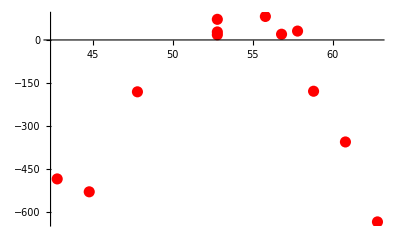
Show[{Plot[(getAxialRock[getSecFreqs[{(κ (Voltage-voltMidPoint))/(√2),(κ (Voltage-voltMidPoint))/(√2),0},massArr,knownSecFreqs,knownMass,numIons,ionPositions]]-maxSecFreq) MHz,{Voltage,-voltRange/2+voltMidPoint,voltRange/2+voltMidPoint},PlotStyle→{Black,Thickness→0.01}],-Graphics-},FrameLabel→{Horizontal Shim Voltages,Secular Freq Shift (Hz)},ImageSize→Large,Frame→{{True,False},{True,False}},GridLines→Automatic]

```mathematica
(*acutal data*)
actualVoltageList = {42.79, 62.79, 52.79, 44.79, 60.79, 47.8, 52.79, 57.8,55.79,52.79, 58.8, 56.8};
offsetSecFreqHz = {-485, -635, 18, -530, -356, -181, 72, 31, 82, 28, -179, 20};
actualData = Transpose@{actualVoltageList, offsetSecFreqHz};
voltRange = Max[actualVoltageList]-Min[actualVoltageList];
voltMidPoint = Mean[actualVoltageList];
nlm = NonlinearModelFit[actualData, -a*(x-b)^2+c,{a,b,c}, x, MaxIterations->1000];
voltMidPoint = ({a,b,c}/. nlm["BestFitParameters"])[[2]];

κ = 1.8;
simVoltageList = Table[Voltage,  {Voltage, -voltRange/2+voltMidPoint, voltRange/2+voltMidPoint,0.1}];
secFreqs = Table[getAxialRock[getSecFreqs[{(κ*(Volt-voltMidPoint))/Sqrt[2],(κ*(Volt-voltMidPoint))/Sqrt[2],0}, massArr, knownSecFreqs, knownMass, numIons, ionPositions]], {Volt, simVoltageList}];
maxSecFreq = Max[secFreqs];


Show[{Plot[(getAxialRock[getSecFreqs[{(κ*(Voltage-voltMidPoint))/Sqrt[2],(κ*(Voltage-voltMidPoint))/Sqrt[2],0}, massArr, knownSecFreqs, knownMass, numIons, ionPositions]]-maxSecFreq)*MHz,
{Voltage, -voltRange/2+voltMidPoint,voltRange/2+voltMidPoint}, PlotStyle->{Black, Thickness->0.01}],
ListPlot[Transpose@{actualVoltageList, offsetSecFreqHz}, PlotStyle->{Red, PointSize[0.02]}]},
FrameLabel->{Style["Horizontal Shim Voltages", 16], Style["Secular Freq Shift (Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic
]
```

NonlinearModelFit::ivar: {860.,2.57262} is not a valid variable.

Plot::plln: Limiting value -10.+NonlinearModelFit[{{42.79,-485},{62.79,-635},{52.79,18},{44.79,-530},{60.79,-356},{47.8,-181},{52.79,72},{57.8,31},{55.79,82},{52.79,28},{58.8,-179},{56.8,20}},{{300000000-860. Plus[«2»]^2,300000000-2.57262 Plus[«2»]^2},{300000000-1050. Plus[«2»]^2,300000000-3.30413 Plus[«2»]^2},{300000000-1200. Plus[«2»]^2,300000000-4.4444 («1»)^2},{300000000-1450. Plus[«2»]^2,300000000-6.64874 Plus[«2»]^2},{300000000-1700. Plus[«2»]^2,300000000-5.63323 Plus[«2»]^2}},{«1»},x,MaxIterations→1000][Be…rs] in {Voltage,«1»,10.+NonlinearModelFit[{{42.79,-485},{62.79,-635},{52.79,18},{44.79,-530},{60.79,-356},{47.8,-181},{52.79,72},{57.8,31},{55.79,82},{52.79,28},{58.8,-179},{56.8,20}},{{300000000-860. Power[«2»],300000000-2.57262 Power[«2»]},{300000000-1050. Power[«2»],300000000-3.30413 Power[«2»]},{300000000-1200. Power[«2»],300000000-«18» Power[«2»]},{300000000-1450. Power[«2»],300000000-6.64874 Power[«2»]},{300000000-1700. Power[«2»],300000000-5.63323 Power[«2»]}},{«1»},x,MaxIterations→1000][…]} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

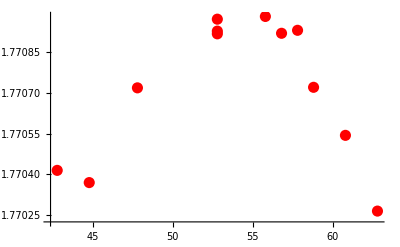
Show[{Plot[getSecFreqs[{(κ (Voltage-voltMidPoint))/(√2),(κ (Voltage-voltMidPoint))/(√2),0},massArr,knownSecFreqs,knownMass,numIons,ionPositions]⟦2⟧⟦9⟧,{Voltage,-voltRange/2+voltMidPoint,voltRange/2+voltMidPoint},PlotStyle→{Black,Thickness→0.01}],-Graphics-},FrameLabel→{Horizontal Shim Voltages,Secular Freq (2π MHz)},ImageSize→Large,Frame→{{True,False},{True,False}},PlotRange→All,GridLines→Automatic]

```mathematica
Show[{Plot[(getSecFreqs[{(κ*(Voltage-voltMidPoint))/Sqrt[2],(κ*(Voltage-voltMidPoint))/Sqrt[2],0}, massArr, knownSecFreqs, knownMass, numIons, ionPositions][[2]][[9]]),
{Voltage, -voltRange/2+voltMidPoint,voltRange/2+voltMidPoint}, PlotStyle->{Black, Thickness->0.01}],
ListPlot[Transpose@{actualVoltageList, offsetSecFreqHz/MHz+1.7709}, PlotStyle->{Red, PointSize[0.02]} ]},
FrameLabel->{Style["Horizontal Shim Voltages", 16], Style["Secular Freq (2π MHz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}}, PlotRange->All,GridLines->Automatic
]
```

### Axial COM Mode Shift

```mathematica
simVoltageList = Table[Voltage,  {Voltage, -voltRange/2+voltMidPoint, voltRange/2+voltMidPoint,0.1}];
secFreqs = Table[getSecFreqs[{(κ*(Volt-voltMidPoint))/Sqrt[2],(κ*(Volt-voltMidPoint))/Sqrt[2],0}, massArr, knownSecFreqs, knownMass, numIons, ionPositions][[2]][[1]], {Volt, simVoltageList}];
maxSecFreq = Max[secFreqs];

Show[{Plot[(getSecFreqs[{(κ*(Voltage-voltMidPoint))/Sqrt[2],(κ*(Voltage-voltMidPoint))/Sqrt[2],0}, massArr, knownSecFreqs, knownMass, numIons, ionPositions][[2]][[1]]- maxSecFreq)*MHz,
{Voltage, -voltRange/2+voltMidPoint,voltRange/2+voltMidPoint}, PlotStyle->{Black, Thickness->0.01}]},
FrameLabel->{Style["Horizontal Shim Voltages", 16], Style["Secular Freq Shift (2π Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic
]
```

NonlinearModelFit::ivar: {860.,2.57262} is not a valid variable.

General::stop: Further output of NonlinearModelFit::ivar will be suppressed during this calculation.

NonlinearModelFit::ivar: {860.,2.57262} is not a valid variable.

Plot::plln: Limiting value -10.+NonlinearModelFit[{{42.79,-485},{62.79,-635},{52.79,18},{44.79,-530},{60.79,-356},{47.8,-181},{52.79,72},{57.8,31},{55.79,82},{52.79,28},{58.8,-179},{56.8,20}},{{300000000-860. Plus[«2»]^2,300000000-2.57262 Plus[«2»]^2},{300000000-1050. Plus[«2»]^2,300000000-3.30413 Plus[«2»]^2},{300000000-1200. Plus[«2»]^2,300000000-4.4444 («1»)^2},{300000000-1450. Plus[«2»]^2,300000000-6.64874 Plus[«2»]^2},{300000000-1700. Plus[«2»]^2,300000000-5.63323 Plus[«2»]^2}},{«1»},x,MaxIterations→1000][Be…rs] in {Voltage,«1»,10.+NonlinearModelFit[{{42.79,-485},{62.79,-635},{52.79,18},{44.79,-530},{60.79,-356},{47.8,-181},{52.79,72},{57.8,31},{55.79,82},{52.79,28},{58.8,-179},{56.8,20}},{{300000000-860. Power[«2»],300000000-2.57262 Power[«2»]},{300000000-1050. Power[«2»],300000000-3.30413 Power[«2»]},{300000000-1200. Power[«2»],300000000-«18» Power[«2»]},{300000000-1450. Power[«2»],300000000-6.64874 Power[«2»]},{300000000-1700. Power[«2»],300000000-5.63323 Power[«2»]}},{«1»},x,MaxIterations→1000][…]} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{Plot[(Part[«2»]⟦1⟧-maxSecFreq) MHz,{Voltage,-voltRange Power[«2»]+voltMidPoint,voltRange Power[«2»]+voltMidPoint},PlotStyle→{Black,Thickness→0.01}]},FrameLabel→{Horizontal Shim Voltages,Secular Freq Shift (2π Hz)},ImageSize→Large,Frame→{{True,False},{True,False}},GridLines→Automatic].

Show[{Plot[(getSecFreqs[{(κ (Voltage-voltMidPoint))/(√2),(κ (Voltage-voltMidPoint))/(√2),0},massArr,knownSecFreqs,knownMass,numIons,ionPositions]⟦2⟧⟦1⟧-maxSecFreq) MHz,{Voltage,-voltRange/2+voltMidPoint,voltRange/2+voltMidPoint},PlotStyle→{Black,Thickness→0.01}]},FrameLabel→{Horizontal Shim Voltages,Secular Freq Shift (2π Hz)},ImageSize→Large,Frame→{{True,False},{True,False}},GridLines→Automatic]

## Axial Rocking Mode Shift Dependence on Single Ion Secular Frequencies

### Scan Wide Range of Secular Frequencies

```mathematica
knownMass = 39.962590863; 
mUnknown = 36;
massArr = {knownMass, mUnknown, knownMass};
eggFreqSpan = Table[eggsFreq, {eggsFreq, 1.200, 3.000,.0025}];
freqShift = Table[SimDiffSecFreqs[.710,eggsFreq-.3,eggsFreq], {eggsFreq, eggFreqSpan}];
shiftData = Transpose@{eggFreqSpan, freqShift};
mass36Plot = ListPlot[shiftData, PlotStyle->{Red, PointSize[0.02]},
FrameLabel->{Style["Single Ca+ EGGs Frequency (MHz)", 16], Style["Secular Freq Shift (Hz) - 36amu", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic]
```

Dot::dotsh: Tensors {0,0,-1,0,0,1,0,0,-1} and {0.852978,0.000506063,-0.0655602,-0.515796,-0.000391801,0.0456692} have incompatible shapes.

Dot::dotsh: Tensors {0,0,-1,0,0,1,0,0,-1} and {0.0162101,-0.0008375,0.741887,-0.00814467,0.000624064,0.670279} have incompatible shapes.

Dot::dotsh: Tensors {0,0,-1,0,0,1,0,0,-1} and {-0.519785,0.0102142,-0.0276587,-0.853137,-0.00581378,0.0328357} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

NonlinearModelFit::ivar: {860.,2.57262} is not a valid variable.

General::stop: Further output of NonlinearModelFit::ivar will be suppressed during this calculation.

$Aborted

Transpose::nmtx: The first two levels of {{1.2,1.2025,1.205,1.2075,1.21,1.2125,1.215,1.2175,1.22,1.2225,1.225,1.2275,1.23,1.2325,1.235,1.2375,1.24,1.2425,1.245,1.2475,1.25,1.2525,1.255,1.2575,1.26,1.2625,1.265,1.2675,1.27,1.2725,1.275,1.2775,1.28,1.2825,1.285,1.2875,1.29,1.2925,1.295,1.2975,1.3,1.3025,1.305,1.3075,1.31,1.3125,1.315,1.3175,1.32,1.3225,«671»},freqShift} cannot be transposed.

ListPlot::lpn: { is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{{1.2,1.2025,1.205,1.2075,1.21,1.2125,1.215,1.2175,1.22,1.2225,1.225,1.2275,1.23,1.2325,1.235,1.2375,1.24,1.2425,1.245,1.2475,1.25,1.2525,1.255,1.2575,1.26,1.2625,1.265,1.2675,1.27,1.2725,1.275,1.2775,1.28,1.2825,1.285,1.2875,1.29,1.2925,1.295,1.2975,1.3,1.3025,1.305,1.3075,1.31,1.3125,1.315,1.3175,1.32,1.3225,1.325,1.3275,1.33,1.3325,1.335,1.3375,1.34,1.3425,1.345,1.3475,1.35,1.3525,1.355,1.3575,1.36,1.3625,1.365,1.3675,1.37,1.3725,1.375,1.3775,1.38,1.3825,1.385,1.3875,1.39,1.3925,1.395,1.3975,1.4,1.4025,1.405,1.4075,1.41,1.4125,1.415,1.4175,1.42,1.4225,1.425,1.4275,1.43,1.4325,1.435,1.4375,1.44,1.4425,1.445,1.4475,1.45,1.4525,1.455,1.4575,1.46,1.4625,1.465,1.4675,1.47,1.4725,1.475,1.4775,1.48,1.4825,1.485,1.4875,1.49,1.4925,1.495,1.4975,1.5,1.5025,1.505,1.5075,1.51,1.5125,1.515,1.5175,1.52,1.5225,1.525,1.5275,1.53,1.5325,1.535,1.5375,1.54,1.5425,1.545,1.5475,1.55,1.5525,1.555,1.5575,1.56,1.5625,1.565,1.5675,1.57,1.5725,1.575,1.5775,1.58,1.5825,1.585,1.5875,1.59,1.5925,1.595,1.5975,1.6,1.6025,1.605,1.6075,1.61,1.6125,1.615,1.6175,1.62,1.6225,1.625,1.6275,1.63,1.6325,1.635,1.6375,1.64,1.6425,1.645,1.6475,1.65,1.6525,1.655,1.6575,1.66,1.6625,1.665,1.6675,1.67,1.6725,1.675,1.6775,1.68,1.6825,1.685,1.6875,1.69,1.6925,1.695,1.6975,1.7,1.7025,1.705,1.7075,1.71,1.7125,1.715,1.7175,1.72,1.7225,1.725,1.7275,1.73,1.7325,1.735,1.7375,1.74,1.7425,1.745,1.7475,1.75,1.7525,1.755,1.7575,1.76,1.7625,1.765,1.7675,1.77,1.7725,1.775,1.7775,1.78,1.7825,1.785,1.7875,1.79,1.7925,1.795,1.7975,1.8,1.8025,1.805,1.8075,1.81,1.8125,1.815,1.8175,1.82,1.8225,1.825,1.8275,1.83,1.8325,1.835,1.8375,1.84,1.8425,1.845,1.8475,1.85,1.8525,1.855,1.8575,1.86,1.8625,1.865,1.8675,1.87,1.8725,1.875,1.8775,1.88,1.8825,1.885,1.8875,1.89,1.8925,1.895,1.8975,1.9,1.9025,1.905,1.9075,1.91,1.9125,1.915,1.9175,1.92,1.9225,1.925,1.9275,1.93,1.9325,1.935,1.9375,1.94,1.9425,1.945,1.9475,1.95,1.9525,1.955,1.9575,1.96,1.9625,1.965,1.9675,1.97,1.9725,1.975,1.9775,1.98,1.9825,1.985,1.9875,1.99,1.9925,1.995,1.9975,2.,2.0025,2.005,2.0075,2.01,2.0125,2.015,2.0175,2.02,2.0225,2.025,2.0275,2.03,2.0325,2.035,2.0375,2.04,2.0425,2.045,2.0475,2.05,2.0525,2.055,2.0575,2.06,2.0625,2.065,2.0675,2.07,2.0725,2.075,2.0775,2.08,2.0825,2.085,2.0875,2.09,2.0925,2.095,2.0975,2.1,2.1025,2.105,2.1075,2.11,2.1125,2.115,2.1175,2.12,2.1225,2.125,2.1275,2.13,2.1325,2.135,2.1375,2.14,2.1425,2.145,2.1475,2.15,2.1525,2.155,2.1575,2.16,2.1625,2.165,2.1675,2.17,2.1725,2.175,2.1775,2.18,2.1825,2.185,2.1875,2.19,2.1925,2.195,2.1975,2.2,2.2025,2.205,2.2075,2.21,2.2125,2.215,2.2175,2.22,2.2225,2.225,2.2275,2.23,2.2325,2.235,2.2375,2.24,2.2425,2.245,2.2475,2.25,2.2525,2.255,2.2575,2.26,2.2625,2.265,2.2675,2.27,2.2725,2.275,2.2775,2.28,2.2825,2.285,2.2875,2.29,2.2925,2.295,2.2975,2.3,2.3025,2.305,2.3075,2.31,2.3125,2.315,2.3175,2.32,2.3225,2.325,2.3275,2.33,2.3325,2.335,2.3375,2.34,2.3425,2.345,2.3475,2.35,2.3525,2.355,2.3575,2.36,2.3625,2.365,2.3675,2.37,2.3725,2.375,2.3775,2.38,2.3825,2.385,2.3875,2.39,2.3925,2.395,2.3975,2.4,2.4025,2.405,2.4075,2.41,2.4125,2.415,2.4175,2.42,2.4225,2.425,2.4275,2.43,2.4325,2.435,2.4375,2.44,2.4425,2.445,2.4475,2.45,2.4525,2.455,2.4575,2.46,2.4625,2.465,2.4675,2.47,2.4725,2.475,2.4775,2.48,2.4825,2.485,2.4875,2.49,2.4925,2.495,2.4975,2.5,2.5025,2.505,2.5075,2.51,2.5125,2.515,2.5175,2.52,2.5225,2.525,2.5275,2.53,2.5325,2.535,2.5375,2.54,2.5425,2.545,2.5475,2.55,2.5525,2.555,2.5575,2.56,2.5625,2.565,2.5675,2.57,2.5725,2.575,2.5775,2.58,2.5825,2.585,2.5875,2.59,2.5925,2.595,2.5975,2.6,2.6025,2.605,2.6075,2.61,2.6125,2.615,2.6175,2.62,2.6225,2.625,2.6275,2.63,2.6325,2.635,2.6375,2.64,2.6425,2.645,2.6475,2.65,2.6525,2.655,2.6575,2.66,2.6625,2.665,2.6675,2.67,2.6725,2.675,2.6775,2.68,2.6825,2.685,2.6875,2.69,2.6925,2.695,2.6975,2.7,2.7025,2.705,2.7075,2.71,2.7125,2.715,2.7175,2.72,2.7225,2.725,2.7275,2.73,2.7325,2.735,2.7375,2.74,2.7425,2.745,2.7475,2.75,2.7525,2.755,2.7575,2.76,2.7625,2.765,2.7675,2.77,2.7725,2.775,2.7775,2.78,2.7825,2.785,2.7875,2.79,2.7925,2.795,2.7975,2.8,2.8025,2.805,2.8075,2.81,2.8125,2.815,2.8175,2.82,2.8225,2.825,2.8275,2.83,2.8325,2.835,2.8375,2.84,2.8425,2.845,2.8475,2.85,2.8525,2.855,2.8575,2.86,2.8625,2.865,2.8675,2.87,2.8725,2.875,2.8775,2.88,2.8825,2.885,2.8875,2.89,2.8925,2.895,2.8975,2.9,2.9025,2.905,2.9075,2.91,2.9125,2.915,2.9175,2.92,2.9225,2.925,2.9275,2.93,2.9325,2.935,2.9375,2.94,2.9425,2.945,2.9475,2.95,2.9525,2.955,2.9575,2.96,2.9625,2.965,2.9675,2.97,2.9725,2.975,2.9775,2.98,2.9825,2.985,2.9875,2.99,2.9925,2.995,2.9975,3.},freqShift}],PlotStyle→{RGBColor[1, 0, 0],PointSize[0.02]},FrameLabel→{Single Ca+ EGGs Frequency (MHz),Secular Freq Shift (Hz) - 36amu},ImageSize→Large,Frame→{{True,False},{True,False}},GridLines→Automatic]

```mathematica
Export["\\\\eric.physics.ucla.edu\\groups\\motion\\Mathematica\\cat_interferometer\\images\\axial_zz_stray_field_shift36.jpg", mass36Plot]
```

\\eric.physics.ucla.edu\groups\motion\Mathematica\cat_interferometer\images\axial_zz_stray_field_shift36.jpg

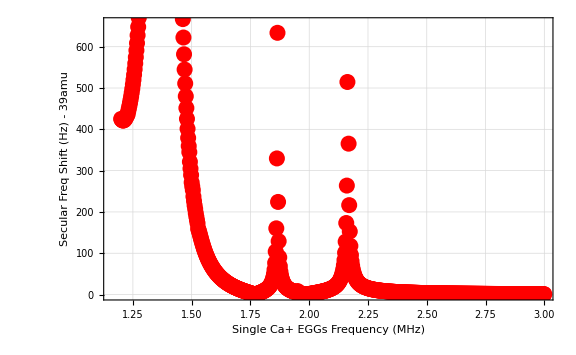

```mathematica
knownMass = 39.962590863; 
mUnknown = 39;
massArr = {knownMass, mUnknown, knownMass};
eggFreqSpan = Table[eggsFreq, {eggsFreq, 1.200, 3.000,.0025}];
freqShift = Table[SimDiffSecFreqs[.710,eggsFreq-.3,eggsFreq], {eggsFreq, eggFreqSpan}];
shiftData = Transpose@{eggFreqSpan, freqShift};
mass39Plot = ListPlot[shiftData, PlotStyle->{Red, PointSize[0.02]},
FrameLabel->{Style["Single Ca+ EGGs Frequency (MHz)", 16], Style["Secular Freq Shift (Hz) - 39amu", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic]
```

```mathematica
SimDiffSecFreqs[.710,1.51-.3,1.51]
```

226.293

```mathematica
Export["\\\\eric.physics.ucla.edu\\groups\\motion\\Mathematica\\cat_interferometer\\images\\axial_zz_stray_field_shift39.jpg", mass39Plot]
```

\\eric.physics.ucla.edu\groups\motion\Mathematica\cat_interferometer\images\axial_zz_stray_field_shift39.jpg

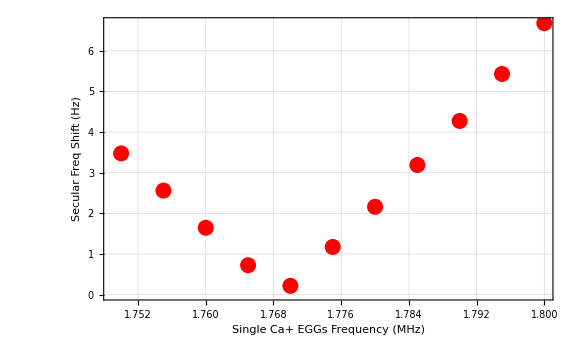

```mathematica
eggFreqSpan = Table[eggsFreq, {eggsFreq, 1.750, 1.800,.005}];
freqShift = Table[SimDiffSecFreqs[.710,eggsFreq-.3,eggsFreq], {eggsFreq, eggFreqSpan}];
shiftData = Transpose@{eggFreqSpan, freqShift};
ListPlot[shiftData, PlotStyle->{Red, PointSize[0.02]},
FrameLabel->{Style["Single Ca+ EGGs Frequency (MHz)", 16], Style["Secular Freq Shift (Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic]
```

### Scan Narrowly about “nulls” where shift vanishes

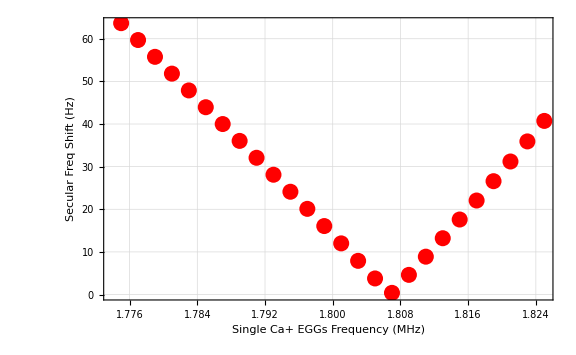

```mathematica
eggFreqSpan = Table[eggsFreq, {eggsFreq, 1.775, 1.825,.002}];
freqShift = Table[SimDiffSecFreqs[.710,eggsFreq-.3,eggsFreq], {eggsFreq, eggFreqSpan}];
shiftData = Transpose@{eggFreqSpan, freqShift};
firstNullPlot = ListPlot[shiftData, PlotStyle->{Red, PointSize[0.02]},
FrameLabel->{Style["Single Ca+ EGGs Frequency (MHz)", 16], Style["Secular Freq Shift (Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic]
```

```mathematica
Export["\\\\eric.physics.ucla.edu\\groups\\motion\\Mathematica\\cat_interferometer\\images\\first_null_plot.jpg", firstNullPlot]
```

\\eric.physics.ucla.edu\groups\motion\Mathematica\cat_interferometer\images\first_null_plot.jpg

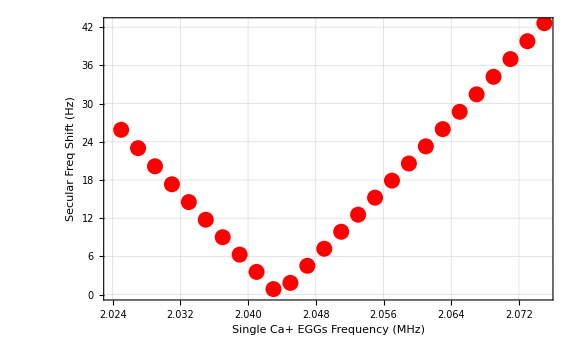

```mathematica
eggFreqSpan = Table[eggsFreq, {eggsFreq, 2.025, 2.075,.002}];
freqShift = Table[SimDiffSecFreqs[.710,eggsFreq-.3,eggsFreq], {eggsFreq, eggFreqSpan}];
shiftData = Transpose@{eggFreqSpan, freqShift};
secondNullPlot = ListPlot[shiftData, PlotStyle->{Red, PointSize[0.02]},
FrameLabel->{Style["Single Ca+ EGGs Frequency (MHz)", 16], Style["Secular Freq Shift (Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic]
```

```mathematica
Export["\\\\eric.physics.ucla.edu\\groups\\motion\\Mathematica\\cat_interferometer\\images\\second_null_plot.jpg", secondNullPlot]
```

\\eric.physics.ucla.edu\groups\motion\Mathematica\cat_interferometer\images\second_null_plot.jpg

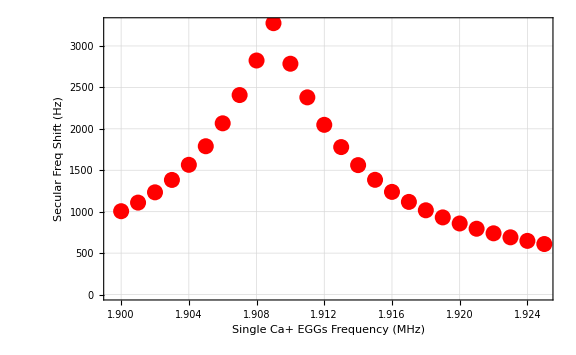

```mathematica
eggFreqSpan = Table[eggsFreq, {eggsFreq, 1.9, 1.925,.001}];
freqShift = Table[SimDiffSecFreqs[.710,eggsFreq-.3,eggsFreq], {eggsFreq, eggFreqSpan}];
shiftData = Transpose@{eggFreqSpan, freqShift};
ListPlot[shiftData, PlotStyle->{Red, PointSize[0.02]},
FrameLabel->{Style["Single Ca+ EGGs Frequency (MHz)", 16], Style["Secular Freq Shift (Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic]
```

### See trend of stray fields and shift caused for different secular frequency configurations

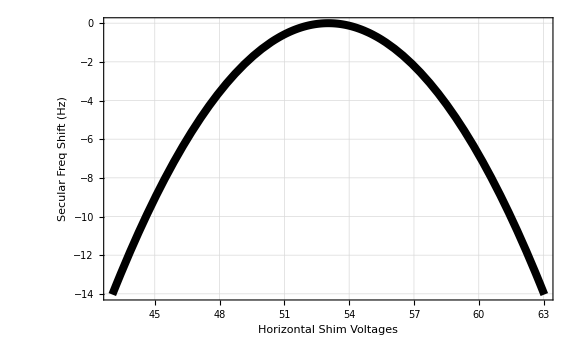

```mathematica
testSecFreqs = 2*π*{.71, 1.5, 1.8}*MHz;
secFreqs = Table[getAxialRock[getSecFreqs[{(κ*(Volt-voltMidPoint))/Sqrt[2],(κ*(Volt-voltMidPoint))/Sqrt[2],0}, massArr, testSecFreqs, knownMass, numIons, ionPositions]], {Volt, simVoltageList}];
maxSecFreq = Max[secFreqs];


Show[{Plot[(getAxialRock[getSecFreqs[{(κ*(Voltage-voltMidPoint))/Sqrt[2],(κ*(Voltage-voltMidPoint))/Sqrt[2],0}, massArr, testSecFreqs, knownMass, numIons, ionPositions]]-maxSecFreq)*MHz,
{Voltage, -voltRange/2+voltMidPoint,voltRange/2+voltMidPoint}, PlotStyle->{Black, Thickness->0.01}]},
FrameLabel->{Style["Horizontal Shim Voltages", 16], Style["Secular Freq Shift (Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic
]
```

```mathematica
testSecFreqs = 2*π*{.71, 1.8, 2.1}*MHz;
secFreqs = Table[getAxialRock[getSecFreqs[{(κ*(Volt-voltMidPoint))/Sqrt[2],(κ*(Volt-voltMidPoint))/Sqrt[2],0}, massArr, testSecFreqs, knownMass, numIons, ionPositions]], {Volt, simVoltageList}];
maxSecFreq = Max[secFreqs];


Show[{Plot[(getAxialRock[getSecFreqs[{(κ*(Voltage-voltMidPoint))/Sqrt[2],(κ*(Voltage-voltMidPoint))/Sqrt[2],0}, massArr, testSecFreqs, knownMass, numIons, ionPositions]]-maxSecFreq)*MHz,
{Voltage, -voltRange/2+voltMidPoint,voltRange/2+voltMidPoint}, PlotStyle->{Black, Thickness->0.01}]},
FrameLabel->{Style["Horizontal Shim Voltages", 16], Style["Secular Freq Shift (Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic
]
```

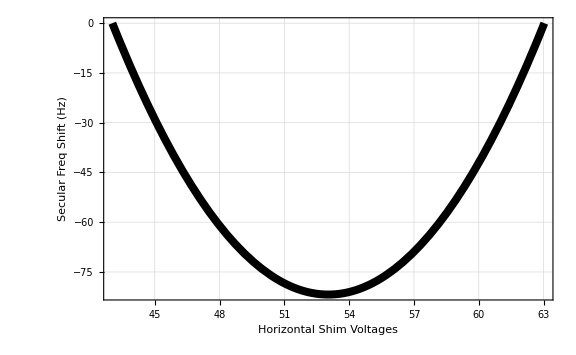

## Anharmonic Calculations

```mathematica
ll[q_, secFreqsMHz_]:= Sqrt[ℏ/(2*2*π*secFreqsMHz[[q]]*MHz)];
quarticDiagonalTerms[nList_, G4_,  secFreqsMHz_, numModes_]:=Sum[ll[i,secFreqsMHz]^4*G4[[i,i,i,i]]*(6*nList[[i]]^2+6*nList[[i]]+3), {i,1,numModes}]
quarticOffDiagonalTerms[nList_, G4_,  secFreqsMHz_, numModes_]:=Sum[6*ll[i, secFreqsMHz]^2*ll[j, secFreqsMHz]^2*G4[[i,i,j,j]]*(2*nList[[i]]+1)*(2*nList[[j]]+1), 
													{i,1,numModes-1},
													{j,i+1,numModes}]
firstOrderPert[nList_, G4_, secFreqsMHz_, numModes_]:= (quarticDiagonalTerms[nList, G4,  secFreqsMHz, numModes] 
													+ quarticOffDiagonalTerms[nList, G4,  secFreqsMHz, numModes]);
```

```mathematica
(*Construct Matrix Elements*)
x3Element[m_, n_]:= (Sqrt[(n+1)*(n+2)*(n+3)]*KroneckerDelta[m, n+3]
								+3*(n+1)^(3/2)*KroneckerDelta[m, n+1]
								+ 3*n^(3/2)*KroneckerDelta[m, n-1]
								+ Sqrt[(n)*(n-1)*(n-2)]*KroneckerDelta[m, n-3]
								);
x2Element[m_, n_]:= (Sqrt[(n+1)*(n+2)]*KroneckerDelta[m,n+2]
					+ (2*n+1)*KroneckerDelta[m, n]
					+ Sqrt[n*(n-1)]*KroneckerDelta[m, n-2]
					);								
x1Element[m_, n_]:= Sqrt[n+1]KroneckerDelta[m,n+1] + Sqrt[n]*KroneckerDelta[m,n-1];	

				
(*Construct Amplitudes*)											
cubicDiagonalTerm[mList_, nList_, G3_, secFreqsMHz_, numModes_]:= Sum[G3[[i,i,i]]*ll[i, secFreqsMHz]^3*
										x3Element[mList[[i]], nList[[i]]]*
										Product[KroneckerDelta[mList[[q]], nList[[q]]], {q, DeleteCases[Range[numModes], i]}]
										,
										{i, 1, numModes}];
cubicOffDiagonalTerm[mList_, nList_, G3_, secFreqsMHz_, numModes_]:= (Sum[3*G3[[i,j,j]]*ll[j, secFreqsMHz]^2*ll[i,secFreqsMHz]
										* x1Element[mList[[i]], nList[[i]]]
										* x2Element[mList[[j]], nList[[j]]]
										* Product[
									        KroneckerDelta[mList[[q]], nList[[q]]],
									        {q, Complement[Range[numModes], {i, j}]}]
									    + 3*G3[[i,i,j]]*ll[i, secFreqsMHz]^2*ll[j, secFreqsMHz]*
										x1Element[mList[[j]], nList[[j]]]* x2Element[mList[[i]], nList[[i]]]
										*  Product[
									        KroneckerDelta[mList[[q]], nList[[q]]],
									        {q, Complement[Range[numModes], {i, j}]}
									     ],
										{i, 1, numModes-1},
										{j, i+1, numModes}
										]
										+ 
										Sum[
										6*G3[[i,j,k]]*ll[i, secFreqsMHz]*ll[j, secFreqsMHz]*ll[k, secFreqsMHz]
										* x1Element[mList[[i]], nList[[i]]]
										* x1Element[mList[[j]], nList[[j]]] 
										* x1Element[mList[[k]], nList[[k]]]
										* Product[
								        KroneckerDelta[mList[[q]], nList[[q]]],
								        {q, Complement[Range[numModes], {i, j, k}]}],
										{i, 1, numModes-2},
										{j, i+1, numModes-1},
										{k, j+1, numModes}]
										);
										
cubicMatrixElement[mList_, nList_, G3_, secFreqsMHz_, numModes_]:= (cubicDiagonalTerm[mList, nList, G3,  secFreqsMHz, numModes] 
																+ cubicOffDiagonalTerm[mList, nList, G3,  secFreqsMHz, numModes]);

secOrderPertEle[mList_, nList_, G3_, secFreqsMHz_, numModes_]:= Abs[cubicMatrixElement[mList, nList, G3,  secFreqsMHz, numModes]]^2/(Total[ℏ*2*π*MHz*secFreqsMHz*nList]-Total[ℏ*2*π*MHz*secFreqsMHz*mList]);
secOrderPert[intermediateStates_, nList_, G3_,  secFreqsMHz_, numModes_]:=Sum[
secOrderPertEle[mList, nList, G3,  secFreqsMHz, numModes], 
{mList, intermediateStates}
]
```

```mathematica
(*Create all connected basis states to a nList*)

createCandidateStates[nList_, numModes_]:=Module[{states},
	states = {};
	(*x3 term all excitations on one mode*);
	Do[
	states = Join[states, 
	Table[
	nList+d*UnitVector[numModes, q], 
	{d, {-3,-1,1,3}}
	]
	],
	{q, 1, numModes}
	];
	(*1 x2 term and 1 x1 term - two excitations on one mode and one excitations one another mode*)
	Do[
	states = Join[states, 
	Catenate @ Table[
	nList
	+di*UnitVector[numModes, q1]
	+dj*UnitVector[numModes, q2],
	{di, {-2,0,2}},
	{dj, {-1,1}}
	]
	],
	{q1, 1, numModes-1},
	{q2, q1+1, numModes}
	];
	Do[
	states = Join[states, 
	Catenate @ Table[
	nList
	+di*UnitVector[numModes, q2]
	+dj*UnitVector[numModes, q1],
	{di, {-2,0,2}},
	{dj, {-1,1}}
	]
	],
	{q1, 1, numModes-1},
	{q2, q1+1, numModes}
	];
	(*3 x1 terms -  all excitations on different modes*);
	Do[
	states = Join[states, 
	Catenate @ Catenate @ Table[
	nList
	+di*UnitVector[numModes, q1]
	+dj*UnitVector[numModes, q2]
	+dk*UnitVector[numModes, q3],
	{di, {-1,1}},
	{dj, {-1,1}},
	{dk, {-1,1}}
	]
	],
	{q1, 1, numModes-2},
	{q2, q1+1, numModes-1},
	{q3, q2+1, numModes}
	];
	states = Select[states, Min[#]>=0 &];
	DeleteDuplicates[states]
	]
```

```mathematica
getPerturbationTensors[EField_, 
massArr_, knownSecFreqs_, knownMass_, numIons_, ionPositions_, β_:0]:=
 Module[
 {massIndepMathieuParams, massIndepSecFreqs, U, evecsNormalized, secFreqsMHz, ionEqPositions,
 coordMasses, U3, A3, B3temp, C3temp, U4, B4temp, C4temp, D4temp},
massIndepMathieuParams= getMathieuParams[knownSecFreqs, knownMass, ΩRF];
massIndepSecFreqs = getMassIndepSecFreqs[massIndepMathieuParams, massArr, ΩRF];
U = getPotential[massArr, massIndepSecFreqs, numIons, EField, ionPositions, β];
coordMasses=Flatten[ConstantArray[#,Length[First[ionPositions]]]&/@ massArr] *amu;
ionEqPositions = getEquilibriumPositions[U, numIons, ionPositions] (*this must be a different name*);
{evecsNormalized, secFreqsMHz} = getModeParams[U, massArr, ionEqPositions, numIons,ionPositions];
U3 = D[U, {Flatten[ionPositions], 3}]/.ionEqPositions;
U4 = D[U, {Flatten[ionPositions], 4}]/.ionEqPositions;
A3 = U3/(3! Sqrt[Outer[Times, coordMasses, coordMasses, coordMasses]]);
A4 = U4/(4! Sqrt[Outer[Times, coordMasses, coordMasses, coordMasses, coordMasses]]);

B3temp = TensorContract[TensorProduct[A3, evecsNormalized], {{1, 5}}];
C3temp = TensorContract[TensorProduct[B3temp, evecsNormalized], {{1, 5}}];
G3 = TensorContract[TensorProduct[C3temp, evecsNormalized], {{1, 5}}];

B4temp = TensorContract[TensorProduct[A4, evecsNormalized], {{1, 6}}];
C4temp = TensorContract[TensorProduct[B4temp, evecsNormalized], {{1, 6}}];
D4temp = TensorContract[TensorProduct[C4temp, evecsNormalized], {{1, 6}}];
G4 = TensorContract[TensorProduct[D4temp, evecsNormalized], {{1, 6}}];
{G3, G4, secFreqsMHz}
]
```

```mathematica
calcSecFreqShifts[nList_, q_, G3_, G4_, secFreqsMHz_]:= Module[{intermediateStates, intermediateStatesExcited, excitedState, shift, numModes},
	numModes = Length[nList];
	excitedState = nList + UnitVector[numModes, q];
	intermediateStates = DeleteCases[createCandidateStates[nList, numModes], nList];
	intermediateStatesExcited = DeleteCases[createCandidateStates[excitedState, numModes], excitedState];
	shift = 
	(firstOrderPert[excitedState, G4, secFreqsMHz, numModes] + secOrderPert[intermediateStatesExcited, excitedState, G3, secFreqsMHz, numModes]) /(2*π*ℏ) 
	- (firstOrderPert[nList, G4, secFreqsMHz, numModes] + secOrderPert[intermediateStates, nList, G3, secFreqsMHz, numModes]) /(2*π*ℏ)
]
```

```mathematica
firstOrderPert[nList, G4, secFreqsMHz, 6]
```

2.2513×10^-34

```mathematica
getSecFreqShifts[EField_, 
massArr_, knownSecFreqs_, knownMass_, numIons_, ionPositions_, nList_, q_:1, β_:0]:=
 Module[
 {shift, G3, G4, secFreqsMHz},
 {G3, G4, secFreqsMHz} = getPerturbationTensors[EField, 
	massArr, knownSecFreqs, knownMass, numIons, ionPositions, β];
shift = calcSecFreqShifts[nList, q, G3, G4, secFreqsMHz]
]
```

### Check Roos (https://arxiv.org/pdf/0705.0788)

```mathematica
knownMass = 39.962590863; 
mUnknown = 36;
knownSecFreqs = 2*π*MHz*{.71, 1.3242, 1.6096}; (*Frequencies from Hao's Calibration on 06-04 - keep these and if need to change override later*)
knownSecFreqs = 2*π*MHz*{1.7, 4, 4}; 
massArr = {knownMass, knownMass};
EField ={0,0,0};
numIons = Length[massArr];
ionPositions = Table[{x[i], y[i], z[i]}, {i, numIons}];
ΩRF = 2*π*19.0696 * MHz;
nList = {0,0,0,0,0,0};
```

```mathematica
{evecsNormalized, secFreqsMHz} = getSecFreqs[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions];

Table[Print[secFreqsMHz[[i]], ": ", evecsNormalized[[i]]], {i, 1, Length[secFreqsMHz]}];
```

1.7: {0,0,0.707107,0,0,0.707107}

2.94449: {0,0,-0.707107,0,0,0.707107}

3.62077: {0.465608,-0.532174,0,-0.465608,0.532174,0}

3.62077: {0.532174,0.465608,0,-0.532174,-0.465608,0}

4.: {-0.514148,-0.48544,0,-0.514148,-0.48544,0}

4.: {-0.48544,0.514148,0,-0.48544,0.514148,0}

{-2.605,-4.28582,-6.03923,-10.0395,-15.9123}

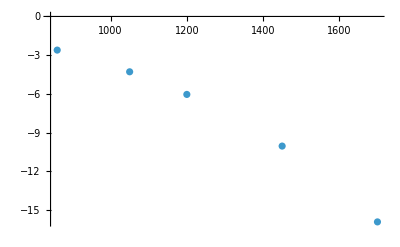

```mathematica
axialSecFreqs = {.86, 1.05, 1.2, 1.45, 1.7};
secShifts = Table[getSecFreqShifts[EField, 
massArr, 2*π*MHz*{axialSecFreqs[[s]], 4, 4}, knownMass, numIons, ionPositions,nList + UnitVector[6,3], 2,0]- 
getSecFreqShifts[EField, massArr, 2*π*MHz*{axialSecFreqs[[s]], 4, 4}, knownMass, numIons, ionPositions,nList, 2,0],{s, 1, Length[axialSecFreqs]}]
a = Thread[{axialSecFreqs(kHz), secShifts}];
ListPlot[a]
```

### Secular Frequency Shift for Ca - HCl - Ca as we Heat Chain

```mathematica
knownMass = 39.962590863; 
mUnknown = 36;
knownSecFreqs = 2*π*MHz*{.71, 1.3242, 1.6096}; (*Frequencies from Hao's Calibration on 06-04 - keep these and if need to change override later*)
massArr = {knownMass, mUnknown, knownMass};
EField ={0,0,0};
numIons = Length[massArr];
ionPositions = Table[{x[i], y[i], z[i]}, {i, numIons}];
ΩRF = 2*π*19.0696 * MHz;
```

```mathematica
{evecsNormalized, secFreqsMHz} = getSecFreqs[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions];

Table[Print[secFreqsMHz[[i]], ": ", evecsNormalized[[i]]], {i, 1, Length[secFreqsMHz]}];
```

0.721858: {0,0,0.59097,0,0,0.549098,0,0,0.59097}

0.880627: {0.511005,0,0,-0.691194,0,0,0.511005,0,0}

1.11777: {-0.707107,0,0,0,0,0,0.707107,0,0}

1.22976: {0,0,0.707107,0,0,0,0,0,-0.707107}

1.2865: {0,-0.529234,0,0,0.663191,0,0,-0.529234,0}

1.40659: {0.488748,0,0,0.72267,0,0,0.488748,0,0}

1.44455: {0,-0.707107,0,0,0,0,0,0.707107,0}

1.69283: {0,-0.468947,0,0,-0.74845,0,0,-0.468947,0}

1.77196: {0,0,-0.388271,0,0,0.835758,0,0,-0.388271}

```mathematica
nList = ConstantArray[0,9]
```

{0,0,0,0,0,0,0,0,0}

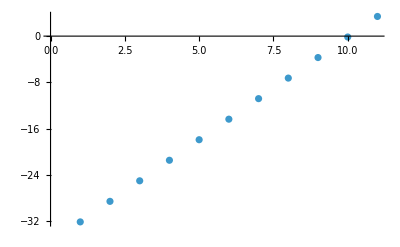

```mathematica
nMax = 10;
nList = ConstantArray[0,9];
secShiftsRock = Table[getSecFreqShifts[EField, 
massArr,knownSecFreqs, knownMass, numIons, ionPositions,nList + s*UnitVector[9, 9], 9,0],{s, 0,nMax}];
Labeled[ListPlot[secShiftsRock],
{"Axial Rocking Secular Frequency Shift", "Phonon Number" }, {Left, Top}, RotateLabel->{True, False}]
```

```mathematica
Total[secShiftsRock[[1;;4]]]
```

-107.082

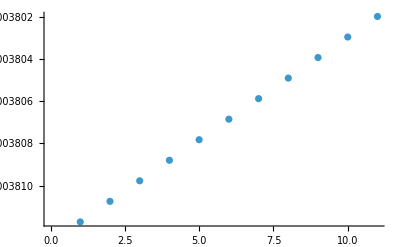

```mathematica
nMax = 10;
nList = ConstantArray[0,9];
secShiftsCOM = Table[getSecFreqShifts[EField, 
massArr,knownSecFreqs, knownMass, numIons, ionPositions,nList + s*UnitVector[9, 1], 1,0],{s, 0,nMax}];
Labeled[ListPlot[secShiftsCOM],
{"Axial COM Secular Frequency Shift", "Phonon Number" }, {Left, Top}, RotateLabel->{True, False}]
```

```mathematica
Total[secShiftsCOM[[1;;4]]]
```

-0.0152411

```mathematica
Expand[Normal[Series[FullSimplify[Series[1/Sqrt[s+(1+ x)^2], {x,0,4}]], {s,0,4}]]]
```

1-s/2+(3 s^2)/8-(5 s^3)/16+(35 s^4)/128-x+(3 s x)/2-(15 s^2 x)/8+(35 s^3 x)/16-(315 s^4 x)/128+x^2-3 s x^2+(45 s^2 x^2)/8-(35 s^3 x^2)/4+(1575 s^4 x^2)/128-x^3+5 s x^3-(105 s^2 x^3)/8+(105 s^3 x^3)/4-(5775 s^4 x^3)/128+x^4-(15 s x^4)/2+(105 s^2 x^4)/4-(525 s^3 x^4)/8+(17325 s^4 x^4)/128